# oglišča

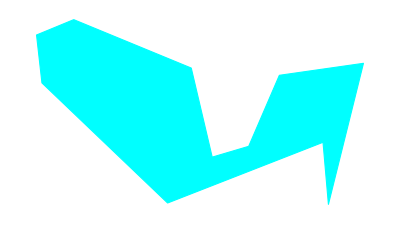

```mathematica
OGLGGB=(#+{3,5})&/@ToExpression[
StringReplace["((-7.5,0.13),
(-0.45831,-2.77501),
(0.79673,-8.11906),
(2.98293,-7.4713),
(4.82,-3.21),
(9.86,-2.49),
(7.76018,-10.95302),
(7.4363,-7.22838),
(-1.87529,-10.87205),
(-9.40554,-3.66569),
(-9.72942,-0.79124))",

{"("->"{",")"->"}"}]
];
Graphics[{
RGBColor[0,1,1,1],
EdgeForm[Thin],

Polygon[OGLGGB]
}]
```

# 3D obračanje

```mathematica
l=5;
velpušč=.015;
debelina=.04;
rm=RotationMatrix[1,{1,2,3}];
OGLGGB3D0=Append[#,0]&/@OGLGGB;
OGLGGB3D=rm.Append[#,0]&/@OGLGGB;
n=l rm.{0,0,1};
velikostčrk=205;
črna=.2;
prozorna=.3;
razmikoznak=.3;
barva1={0,0,1,.4};
barva2={0,1,1,1};
barva3={0,0,0,.3};
rkot=4;
stranickot=100;
debelinastr=.001;


grafika=Show[


(*polskvi*)
Graphics3D[{
RGBColor[barva1],
EdgeForm[Thickness[debelinastr]],

Polygon[OGLGGB3D]
}],
Graphics3D[{
RGBColor[barva2],
EdgeForm[Thickness[debelinastr]],

Polygon[OGLGGB3D0]
}],



(*vektorja*)
Graphics3D[{
RGBColor[barva1],
Text[MaTeX["\\color{blue}{\\hat{n}}",FontSize->velikostčrk],(1+razmikoznak/l)n],
Arrowheads[velpušč],

Arrow[Tube[{{0,0,0},n},
debelina]]
}],

Graphics3D[{
RGBColor[barva2],
Text[MaTeX["\\color{cyan}{\\mathbf{\\left(0,0,1\\right)}}",FontSize->velikostčrk],{0,0,l+razmikoznak}],
Arrowheads[velpušč],

Arrow[Tube[{{0,0,0},l {0,0,1}},
debelina]]
}],
(*kot*)

Graphics3D[{
Text[MaTeX["\\color{siva}{RM\\cdot}",FontSize->velikostčrk],(rkot+.4) RotationMatrix[.5*1,{1,2,3}].{0,0,1}],
	RGBColor[barva3],
	Arrowheads[velpušč],
	Arrow[
	Tube[
	Table[
rkot RotationMatrix[delež*1,{1,2,3}].{0,0,1},
{delež,1,0,-1/stranickot}]
, debelina]]}],






(*nastavitve*)
ImageSize->6{1920,1080},
Boxed->False,
ViewVertical->{0,0,1},
ViewPoint-> .2{5,-100,30},
Lighting->"Neutral"

];
Export["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\fiz\\rn.aviončki\\grafi\\obračanje ploskve iz 2D v 3D0.png",grafika]
```

c:\Users\gal\Documents\ŠOLA\NAR\fiz\rn.aviončki\grafi\obračanje ploskve iz 2D v 3D0.png

```mathematica
SystemOpen["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\fiz\\rn.aviončki\\grafi\\obračanje ploskve iz 2D v 3D0.png"]
```

```mathematica
SystemOpen["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\fiz\\rn.aviončki\\grafi\\obračanje ploskve iz 2D v 3D0.png"]
```

# samo prazen 2D

```mathematica
grafika=Show[
Graphics[{
RGBColor[0,1,1,1],
EdgeForm[Thickness[.001]],

Polygon[OGLGGB]
}],
ImageSize->4*1920
];
Export["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\fiz\\rn.aviončki\\grafi\\grafi\\triangulacija0.png",grafika]
```

c:\Users\gal\Documents\ŠOLA\NAR\fiz\rn.aviončki\grafi\grafi\triangulacija0.png

```mathematica
SystemOpen["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\fiz\\rn.aviončki\\grafi\\grafi\\triangulacija0.png"]
```

```mathematica
SystemOpen["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\fiz\\rn.aviončki\\grafi\\grafi\\triangulacija0.png"]
```

# razdelitev

```mathematica
grafika=Show[
Graphics[{
RGBColor[0,1,1,1],
EdgeForm[Thickness[.001]],

Polygon[OGLGGB]
}],
Graphics[{
RGBColor[{1,0,0}],
Thickness[.001],

Line[#]
}]&/@({OGLGGB[[#[[1]] ]],OGLGGB[[#[[2]] ]]}&/@{
{6,8},
{5,8},
{4,8},
{3,8},
{3,1},
{3,-1},
{3,-2},
{3,-3}
}),
Graphics[{
RGBColor[{0,0,0}],
Arrowheads[.02],
Thickness[.003],

Arrow[
dhbhsb=OGLGGB[[# ]]&/@{-3,-4};
{dhbhsb[[1]],dhbhsb[[1]]+.2(dhbhsb[[2]]-dhbhsb[[1]])}
]
}],
Graphics[{
Text[MaTeX["\\color{črna}{Z}",FontSize->193.5],OGLGGB[[-3]]+{0,-.5}],
RGBColor[{0,0,0}],
Disk[OGLGGB[[-3]],.06]
}],


ImageSize->4*1920
];
Export["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\fiz\\rn.aviončki\\grafi\\triangulacija1.png",grafika]
```

c:\Users\gal\Documents\ŠOLA\NAR\fiz\rn.aviončki\grafi\triangulacija1.png